```mathematica
c1 = RGBColor["#FF6F59"];
c2 = RGBColor["#7A306C"];
c3 = RGBColor["#668F80"];
c4 = RGBColor["#59C9A5"];
c5 = RGBColor["#48BEFF"];
```

# Boosted Dark Matter Fluxes

## Interactions of Cosmic Rays with intergalactic and atmospheric baryons to produce boosted dark matter

## Reproducing the Pospelov Results

### Calculations

We define the maximum and minimum energy functions that arise from the kinematics,

```mathematica
Tmax[Ti_, mi_, mchi_] =  (Ti^2+2mi Ti)/(Ti+(mi+mchi)^2/(2mchi));
Tmin[Tchi_, mi_, mchi_] = If[Tchi ≥ 2mi, If[Tchi > 2mi, (Tchi/2-mi)(1+(1 + (2Tchi)/mchi (mi + mchi)^2/(2mi - Tchi)^2)^(1/2)), 0], 
								(Tchi/2-mi)(1-(1 + (2Tchi)/mchi (mi + mchi)^2/(2mi - Tchi)^2)^(1/2))] ;
```

Next we parametrise the cosmic ray flux for both the protons and the Helium components using the values in the table. For protons this is;

```mathematica
(*proton*)
Fp[R_] := Module[
	{a0,a1,a2,a3,a4,a5,b,c,d1,d2,e1,e2,f1,f2,g,Fp1,Fp2},
	{a0,a1,a2,a3,a4,a5}={94.1,-831,0,16700,-10200,0};
	{b,c,d1,d2,e1,e2,f1,f2,g}={10800,8590,-4230000,3190,274000,17.4,-39400,0.464,0};
	Fp1=a0+a1*R+a2*R^2+a3*R^3+a4*R^4+a5*R^5;
	Fp2=b+c/R+d1/(d2+R)+e1/(e2+R)+f1/(f2+R)+g*R;
	If[R≤ 1,If[R ≥ 0.2, 10^-4 Fp1/R^2.7, 0], 10^-4 Fp2/R^2.7]
]
```

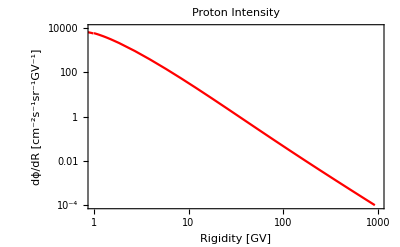

```mathematica
LogLogPlot[10^4*Fp[R], {R, 0.001, 10^5},Frame->True,FrameLabel->{"Rigidity [GV]","dϕ/dR [cm^-2s^-1sr^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Proton Intensity", PlotStyle -> {Red}, PlotRange->{{1, 10^3},{10^-4, 10^4}}]
```

Note that this increases for rigidities below 0.2 GV. To compensate for this we should introduce a minimum rigidity below which we do not trust the parametrisation. We choose this to be 0.2 GV for the proton flux.

```mathematica
minRp = 0.2;
```

We carry out the same parametrisation for Helium;

```mathematica
(*helium*)
Rcut = 1.9;
Fh[R_] := Module[
	{a0,a1,a2,a3,a4,a5,b,c,d1,d2,e1,e2,f1,f2,g,Fh1,Fh2},
	{a0,a1,a2,a3,a4,a5}={1.14,0,-118,578,0,-87};
	{b,c,d1,d2,e1,e2,f1,f2,g}={3120,-5530,3370,1.29,134000,88.5,-1170000,861,0.03};
	Fh1=a0+a1*R+a2*R^2+a3*R^3+a4*R^4+a5*R^5;
	Fh2=b+c/R+d1/(d2+R)+e1/(e2+R)+f1/(f2+R)+g*R;
	If[R≤ Rcut,If[R ≥ 0.2, 10^-4 Fh1/R^2.7, 0],10^-4 Fh2/R^2.7]
]
```

We have also extended the range of validity for the Fh1 expression slightly above 1 GV to avoid the awkward feature at 1 GV.

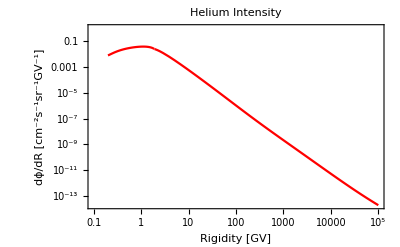

```mathematica
LogLogPlot[{10^4*Fh[R]}, {R, 0.1, 10^5},Frame->True,FrameLabel->{"Rigidity [GV]","dϕ/dR [cm^-2s^-1sr^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Helium Intensity", PlotStyle -> {Red}, PlotRange->]
```

Comparing the two fluxes, we see;

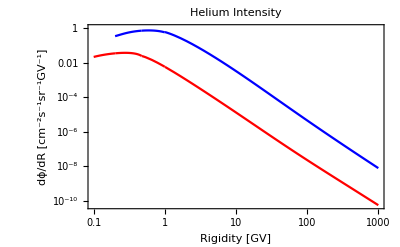

```mathematica
LogLogPlot[{Fp[R], Fh[4*R]}, {R, 0.1, 10^3},Frame->True,FrameLabel->{"Rigidity [GV]","dϕ/dR [cm^-2s^-1sr^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Helium Intensity", PlotStyle -> {Blue,Red}]
```

This has the similar issue of starting to increase again below approximately 0.2 GV. As such we include a global rigidity cut off below which we do not assume validity of this parametrisation. We can implement this directly into the intensities by setting a hard cut off such that the intensity is assumed to be zero below this point.

```mathematica
minR = 0.2;
```

The rigidity can then be defined in terms of the energy;

```mathematica
R[A_,Z_,T_,T0_] = A/Z(T^2 + 2 T T0)^(1/2);
```

Where T_0 is the proton or helium rest mass. In units of GeV/c^2 these are given by;

```mathematica
mp = 0.9383; (* in GeV *)
mh = 4.03188 * 0.932; (* 4.03188 u *)
```

With the rigidity definition above, we can compute the differential cosmic ray flux dϕ_i/dT_i for both the proton component and Helium,

```mathematica
Rp[T_] = R[1, 1, T, mp];
dRp[T_] = D[Rp[T], T];
Rh[T_] = R[4, 2, T, mh];
dRh[T_] = D[Rh[T], T];
dPpdTi[Ti_] := 4 Pi Fp[Rp[Ti]] dRp[Ti];
dPhdTi[Ti_] := 4 Pi Fh[Rh[Ti]] dRh[Ti];
```

```mathematica
Solve[R[A, Z, T, T0] == Rs, T]
```

{{T→-T0-(√(A^2 T0^2+Rs^2 Z^2))/A},{T→-T0+(√(A^2 T0^2+Rs^2 Z^2))/A}}

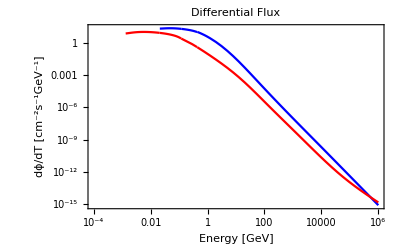

```mathematica
LogLogPlot[{dPpdTi[T], dPhdTi[T]}, {T, 10^-4, 10^6},Frame->True,FrameLabel->{"Energy [GeV]","dϕ/dT [cm^-2s^-1GeV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Differential Flux", PlotStyle -> {Blue,Red}]
```

To obtain the final expression, we need to compute the form factors, note that the Λ_i are quoted in GeV.

```mathematica
Λp = 0.770;
Λh = 0.410;
Gp[x_] = (1+x/Λp^2)^-2;
Gh[x_] = (1+x/Λh^2)^-2;
```

For given choices of D_eff, ρ_loc, m_χ and σ_χ, we can now compute dϕ_χ/dT_χ as;

```mathematica
dPchidTchiProton[Tchi_, Deff_, ρ_, mchi_, σ_] := (Deff ρ σ)/mchi(Gp[2 mchi Tchi]^2 NIntegrate[dPpdTi[Ti]/Tmax[Ti, mp, mchi], {Ti, Tmin[Tchi, mp, mchi], Infinity}]);
```

```mathematica
dPchidTchiBoth[Tchi_, Deff_, ρ_, mchi_, σ_] := (Deff ρ σ)/mchi(Gp[2 mchi Tchi]^2 NIntegrate[dPpdTi[Ti]/Tmax[Ti, mp, mchi], {Ti, Tmin[Tchi, mp, mchi], Infinity}] + Gh[2 mchi Tchi]^2 NIntegrate[dPhdTi[Ti]/Tmax[Ti, mh, mchi], {Ti, Tmin[Tchi, mh, mchi], Infinity}]);
```

We can now try and generate the plot as shown in Fig. 1. We choose some relevant values;

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ti near {Ti} = {0.0235331}. NIntegrate obtained 14055. and 43.6271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ti near {Ti} = {0.0235331}. NIntegrate obtained 14055. and 43.6271 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ti near {Ti} = {0.023512}. NIntegrate obtained 1438.08 and 4.45743 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

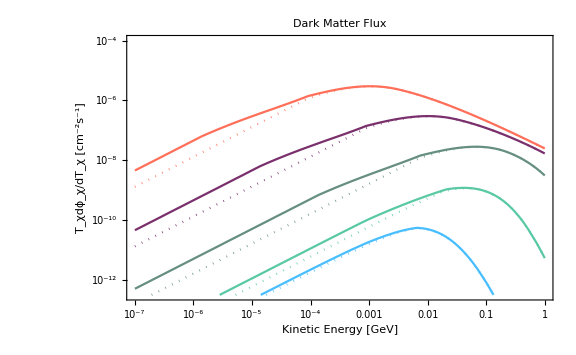

```mathematica
Deff=0.997 3.086 10^21; (* in cm *)
σ =10^-30; (* in cm^2 *)
mchi1 = 0.001; (* in GeV *)
mchi2=0.01;
mchi3 =0.1;
mchi4=1;
mchi5=10;
ρ=0.3; (* in GeV cm^-3 *)
LogLogPlot[{Tchi dPchidTchiBoth[Tchi, Deff, ρ, mchi1, σ],Tchi dPchidTchiProton[Tchi, Deff, ρ, mchi1, σ], 
Tchi dPchidTchiBoth[Tchi, Deff, ρ, mchi2, σ],
Tchi dPchidTchiProton[Tchi, Deff, ρ, mchi2, σ], 
Tchi dPchidTchiBoth[Tchi, Deff, ρ, mchi3, σ], 
Tchi dPchidTchiProton[Tchi, Deff, ρ, mchi3, σ], 
Tchi dPchidTchiBoth[Tchi, Deff, ρ, mchi4, σ], 
Tchi dPchidTchiProton[Tchi, Deff, ρ, mchi4, σ], 
Tchi dPchidTchiBoth[Tchi, Deff, ρ, mchi5, σ], 
Tchi dPchidTchiProton[Tchi, Deff, ρ, mchi5, σ]}, 
{Tchi, 10^-7, 10^0},
PlotRange->{{10^-7,10^0},{10^-12.5,10^-4}},
Frame->True,
FrameLabel->{"Kinetic Energy [GeV]"," T_χdϕ_χ/dT_χ [cm^-2s^-1]"},
LabelStyle->FontSize->16,PlotLabel->"Dark Matter Flux", 
PlotStyle -> {c1, {c1, Dotted}, c2, {c2, Dotted}, c3, {c3, Dotted}, c4, {c4, Dotted}, c5, {c5, Dotted}}, 
ImageSize->Large]
```

-Graphics-

## Atmospheric Contribution

We are now interested in calculating the atmospheric contribution to the dark matter flux. This is because CRMC simulations of the proton-proton interactions in the interstellar medium seem to result in a negligible flux of the order of the m_χ=0.01 GeV line in the Pospelov case. To begin, we take the AMS results from PRL 114, 171103 (2015) as shown below;

-Graphics-

The parametrisation for 45 GV ≤ R ≤ 1.8 TV is given by;

-Graphics-

where the best fit parameter values are;

C=0.4544 m^-2 sr^-1 s^-1 GV^-1

γ =-2.849

Δγ=0.133

s=0.024

R_0= 336 GV

We can now check this parametrisation across the range given;

```mathematica
(* proton flux, R in GV*)
FpA[R_]:= Module[
	{C, γ, dγ, s, R0, FpA},
	{C, γ, dγ, s, R0} = {0.4544, -2.849, 0.133, 0.024, 336.0};
	FpA = C (R/45)^γ (1 + (R/R0)^(dγ/s))^s;
	If[45.0 ≤ R ≤ 1800.0, FpA, 0.0]  
]
```

```mathematica
Rtilde[Rmin_, Rmax_] := (1/(3.7 (Rmax - Rmin))*(Rmax^3.7 - Rmin^3.7))^(1/2.7);
```

```mathematica
8.212*10^-6 - FpA[Rtilde[175, 192]]*10^-3
```

-6.64664×10^-8

```mathematica
atmosphereFlux = Import["/home/k1893416/allMyStuff/BoostedDM/data/atmosphere_flux.csv", "CSV", "HeaderLines"-> 0]
atmosphereFluxScaled = Import["/home/k1893416/allMyStuff/BoostedDM/data/atmosphere_scaled.csv", "CSV", "HeaderLines"-> 0];
```

Import::nffil: File not found during Import.

$Failed

Import::nffil: File not found during Import.

General::sfunc: {{Log,Exp},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

General::sfunc: {{Log,Exp},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

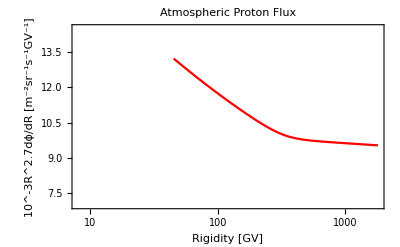
Show[ListLogLinearPlot[$Failed,Frame→True,PlotRange→{{8,1800.},{7,14.5}},FrameLabel→{Rigidity [GV],10^-3R^2.7dϕ/dR [m^-2sr^-1s^-1GV^-1]},LabelStyle→FontSize→16,PlotLabel→Atmospheric Proton Flux,PlotStyle→{RGBColor[0, 1, 0]}],ListLogLinearPlot[$Failed,Frame→True,PlotRange→{{8,1800.},{7,14.5}},FrameLabel→{Rigidity [GV],10^-3R^2.7dϕ/dR [m^-2sr^-1s^-1GV^-1]},LabelStyle→FontSize→16,PlotLabel→Atmospheric Proton Flux,PlotStyle→{RGBColor[0, 0, 1]}],-Graphics-]

```mathematica
dataOne =ListLogLinearPlot[atmosphereFlux, Frame->True, PlotRange->{{8, 1.8 10^3}, {7, 14.5}},FrameLabel->{"Rigidity [GV]","10^-3R^2.7dϕ/dR [m^-2sr^-1s^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Atmospheric Proton Flux", PlotStyle -> {Green}];
dataTwo = ListLogLinearPlot[atmosphereFluxScaled, Frame->True, PlotRange->{{8, 1.8 10^3}, {7, 14.5}},FrameLabel->{"Rigidity [GV]","10^-3R^2.7dϕ/dR [m^-2sr^-1s^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Atmospheric Proton Flux", PlotStyle -> {Blue}];
plt = LogLinearPlot[10^-3 R^2.7 FpA[R], {R, 45, 1800},Frame->True, PlotRange->{{8, 1.8 10^3}, {7, 14.5}},FrameLabel->{"Rigidity [GV]","10^-3R^2.7dϕ/dR [m^-2sr^-1s^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Atmospheric Proton Flux", PlotStyle -> {Red}];
Show[dataOne, dataTwo, plt]
```

We want to extend this down to at least